# Fairing and Simplification

CSE 554 Module 4, Washington University in St. Louis (Fall 2023)

## Introduction

Fairing and simplification are among the most common tasks performed on a polyline (or triangular mesh) extracted from a digital image (or volume). You will implement the classical centroid-averaging algorithm for fairing, and the edge-collapsing algorithm for simplification, both in 2D and 3D. The 3D implementation of edge-collapsing is optional, but will earn you extra credits.

## Helpers

Sets the default folder to be the folder where this notebook is saved.

```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
```

### Showing polylines

This function displays a 2D curve represented as a polyline {V,E}, where V is a list of vertex coordinates (with X,Y components), and E is a list of edges, each consisting of the indices of its two vertices. The function takes in an additional parameter of color (e.g., GrayLevel or RGB).

```mathematica
showCurve[{V_,E_},col_]:=Graphics[{{col,{Map[Line[V⟦#⟧]&,E]}},Map[Point,V]},Frame->False];
```

Same as above, except the vertices will not be displayed. This is helpful if you have lots of vertices in the curve.

```mathematica
showCurveNoPoints[{V_,E_},col_]:=Graphics[{col,Map[Line[V⟦#⟧]&,E]},Frame->False];
```

### Showing meshes

This function displays a 3D surface represented as a polygonal mesh {V,T}, where V is a list of vertex coordinates (with X,Y,Z components), and T is a list of polygons, each consisting of the indices of its vertices. The function takes in an additional parameter of color (e.g., GrayLevel or RGB).

```mathematica
showSurface[{V_,T_},col_]:=Graphics3D[{col,Map[Polygon[V⟦#⟧]&,T]},RotationAction->Clip,Lighting->"Neutral",Boxed->False];
```

Same as agove, except the polygon edges will not be displayed. This is helpful if you have lots of polygons in the surface.

```mathematica
showSurfaceNoEdges[{V_,T_},col_]:=Graphics3D[{col,EdgeForm[{}],Map[Polygon[V⟦#⟧]&,T]},RotationAction->Clip,Lighting->"Neutral",Boxed->False];
```

Same as agove, except ONLY the polygon edges will be displayed (i.e., a wire-frame). This is helpful when you want to show two surfaces at the same time (e.g., one showing only edges).

```mathematica
showSurfaceEdgesOnly[{V_,T_},col_]:=Graphics3D[{col,Map[Line[Append[V⟦#⟧,Last[V⟦#⟧]]]&,T]},RotationAction->Clip,Lighting->"Neutral",Boxed->False];
```

## Your task

### Smoothing (2D) [3 pts]

Algorithm 1: [2 pts] 2D smoothing: Create a function that takes in a polyline (curve), two constants (λ and κ), an integer (num), and output a smoothed polyline faired using the non-shrinking mid-point averaging algorithm for a total of 2×num iterations (in which the odd iterations use interpolation parameter λ and even iterations use 1/(κ-1/λ)). Both the input and output polylines should be represented as a polyline {V,E}, where V is a list of vertex coordinates (with X,Y components), and E is a list of edges, each consisting of the indices of its two vertices. 

Note: You might find it helpful to write a helper function that performs one iteration of smoothing with a given interpolation parameter. Debug this helper function first before calling it in your final fairing function with specific parameter at each iteration.

```mathematica
(*Assume edge is 1D array of indices of vertices of poly*)
getVerts[poly_,edge_]:=Module[
{verts},
verts=Table[0,{Length[edge]}];
Do[verts[[x]]=poly[[1,edge[[x]]]],{x,Length[edge]}];
Return[verts];
];
```

```mathematica
fair2D[curve_,λ_,κ_,num_]:=Module[
{dim,numEdges,currEdge,currVerts,table,currCurve,nextCurve},
dim=Dimensions[curve];
numEdges=Length[curve[[2]]];
table=Table[False,Length[curve[[1]]]];
currCurve=curve;
nextCurve=Table[0,dim[[1]],dim[[2]],dim[[3]]];
nextCurve[[2]]=currCurve[[2]];
Do[
(*Do iteration*)
Do[
(*Get current edge and vertices*)
currEdge=currCurve[[2,x]];
currVerts=getVerts[currCurve,currEdge];

If[table[[currEdge[[1]]]],
(*There is another value stored so we can take average and replace vertex*)
If[EvenQ[y],
nextCurve[[1,currEdge[[1]]]]=(1-1/(κ-1/λ))*currCurve[[1,currEdge[[1]]]]+((nextCurve[[1,currEdge[[1]]]]+currVerts[[2]])/2)*1/(κ-1/λ);
,
nextCurve[[1,currEdge[[1]]]]=(1-λ)*currCurve[[1,currEdge[[1]]]]+((nextCurve[[1,currEdge[[1]]]]+currVerts[[2]])/2)*λ;
];
,
(*There is no value stored so just store it in hash table*)
nextCurve[[1,currEdge[[1]]]]=currVerts[[2]];
table[[currEdge[[1]]]]=True;
];
If[table[[currEdge[[2]]]],
(*There is another value stored so we can take average and replace vertex*)
If[EvenQ[y],
nextCurve[[1,currEdge[[2]]]]=(1-1/(κ-1/λ))*currCurve[[1,currEdge[[2]]]]+((nextCurve[[1,currEdge[[2]]]]+currVerts[[1]])/2)*1/(κ-1/λ);
,
nextCurve[[1,currEdge[[2]]]]=(1-λ)*currCurve[[1,currEdge[[2]]]]+((nextCurve[[1,currEdge[[2]]]]+currVerts[[1]])/2)*λ;
];
,
(*There is no value stored so just store it in hash table*)
nextCurve[[1,currEdge[[2]]]]=currVerts[[1]];
table[[currEdge[[2]]]]=True;
];
,
{x,numEdges}
];

(*Update current and next curve*)
table=Table[False,Length[curve[[1]]]];
currCurve = nextCurve;
nextCurve=Table[0,dim[[1]],dim[[2]],dim[[3]]];
nextCurve[[2]]=currCurve[[2]];
,
{y,2*num}
];

Return[currCurve]
];
```

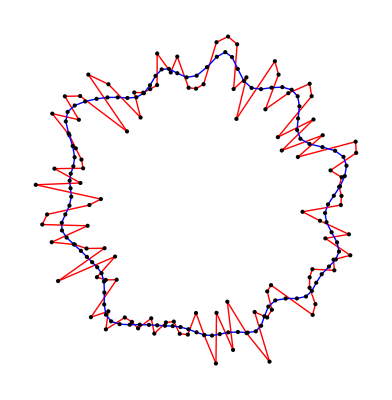

```mathematica
Show[showCurve[circleBumpy,Red],showCurve[fair2D[circleBumpy,0.5,0.1,25],Blue]]
```

Testing: [1 pt] Test your algorithm on the following example (a bumpy circle).  Some suggestions for testing:

1. Start with a small numPoints (e.g., 10) on the circle, and gradually go up. Visualize your result using showCurve (see Helpers), and display both your result and the original curve using Show. Your results should be identical to the pictures below, where the red curves are the original ones (left: 20 points; right: 100 points), and the blue curves have been smoothed after 50 iterations using λ=.5 and κ=.1.

2. Create a Manipulate applet that allows you to dynamically change number of iterations, λ, and κ, and displays the results. Observe how the result changes with these parameters.

```mathematica
numPoints=20;SeedRandom[0];
circleBumpy={N[Table[{Cos[2π/numPoints*i],Sin[2π/numPoints*i]}*RandomReal[{0.7,1.3}],{i,numPoints}]],Table[{i,Mod[i,numPoints]+1},{i,numPoints}]};
```

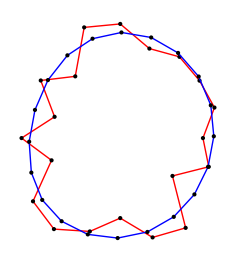
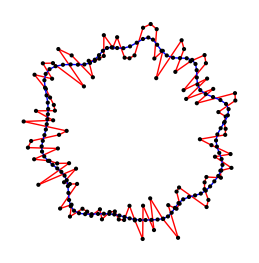

```mathematica
Points20=20;SeedRandom[0];
circleBumpy20={N[Table[{Cos[2π/Points20*i],Sin[2π/Points20*i]}*RandomReal[{0.7,1.3}],{i,Points20}]],Table[{i,Mod[i,Points20]+1},{i,Points20}]};
Points100=100;SeedRandom[0];
circleBumpy100={N[Table[{Cos[2π/Points100*i],Sin[2π/Points100*i]}*RandomReal[{0.7,1.3}],{i,Points100}]],Table[{i,Mod[i,Points100]+1},{i,Points100}]};
```

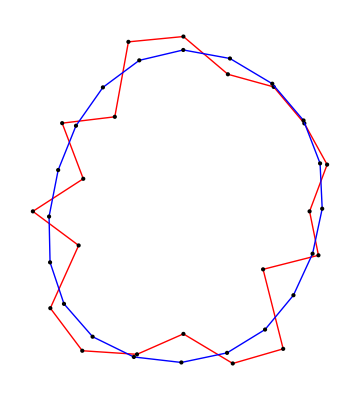

```mathematica
Show[showCurve[circleBumpy20,Red],showCurve[fair2D[circleBumpy20,0.5,0.1,25],Blue]]
```

```mathematica
Show[showCurve[circleBumpy100,Red],showCurve[fair2D[circleBumpy100,0.5,0.1,25],Blue]]
```

-Graphics-

```mathematica
testSmooth2D[curve1_,curve2_]:=Manipulate[
If[toggle,
Show[showCurve[curve2,Red],showCurve[fair2D[curve2,λ,κ,num],Blue]],
Show[showCurve[curve1,Red],showCurve[fair2D[curve1,λ,κ,num],Blue]]],
{λ,0.1,1,0.1},{κ,0,1,0.1},{num,1,25,1},{{toggle,False,"Use 100 Points"},{True,False}}
];
```

```mathematica
testSmooth2D[circleBumpy20,circleBumpy100]
```

### Smoothing (3D) [3 pts]

Algorithm 2: [2 pts] 3D smoothing: Create a function that takes in a 3D mesh (surface), two constants (λ and κ), an integer (num), and output a smoothed mesh faired using the non-shrinking centroid averaging algorithm for a total of 2×num iterations. Both the input and output meshes should be represented as a triangular mesh {V,T}, where V is a list of vertex coordinates (with X,Y,Z components), and T is a list of triangles, each consisting of the indices of its three vertices.

Note: As in 2D, write a helper function that performs one iteration of smoothing, and debug it before calling it in your fairing function.

```mathematica
(*Get ring of indices that is around all vertices*)
getRing[surface_]:=Module[
{numVerts,ring,selection},
numVerts=CountDistinct[Flatten[surface[[2]]]];
ring=Table[0,{numVerts}];
Do[
selection=Select[surface[[2]],MemberQ[#,x]&];
ring[[x]]=DeleteCases[Union[Flatten[selection]],x];
,
{x,numVerts}
];
Return[ring];
];
```

```mathematica
fair3D[surface_,λ_,κ_,num_]:=Module[
{dim,numVerts,ring,currSurface,nextSurface,sum},
dim=Dimensions[surface][[1]];
numVerts=CountDistinct[Flatten[surface[[2]]]];
currSurface=surface;
nextSurface=Table[0,dim];
nextSurface[[1]]=Table[0,Length[surface[[1]]]];
nextSurface[[2]]=surface[[2]];
ring=getRing[surface];

Do[
(*One iteration*)
Do[
sum=0;
Do[sum=sum+currSurface[[1,ring[[x,y]]]],{y,Length[ring[[x]]]}];
If[EvenQ[z],
nextSurface[[1,x]]=(1-1/(κ-1/λ))*currSurface[[1,x]]+(1/(κ-1/λ))*sum/Length[ring[[x]]];
,
nextSurface[[1,x]]=(1-λ)*currSurface[[1,x]]+λ*sum/Length[ring[[x]]];
];
,
{x,numVerts}
];

(*Update current and next surface*)
currSurface = nextSurface;
,
{z,2*num}
];
Return[currSurface];
];
```

Testing: [1 pt] Test your algorithm on the bumpy spheres in files "sphereBumpy_small.txt" and "sphereBumpy_big.txt" (load them using Get; they are already in our mesh format). Follow similar steps in the 2D test:

1. Debug your code first with the small bumpy sphere before moving on to the larger sphere. Visualize your result using showSurface (see Helpers), and display both your result and the original surface by showing the original in wire-frame mode (using showSurfaceEdgesOnly in Helpers). Your result should look like the pictures below, where the red surfaces and wireframes are the original inputs (first row: small sphere; second row: large sphere), and the gray surfaces have been smoothed after 20 iterations using λ=.5 and κ=.1.

2. Create a Manipulate applet that allows you to dynamically change the number of iterations, λ, and κ, and displays the results. Observe how the result changes with these parameters.

```mathematica
sphereBumpySmall=Get["sphereBumpy_small.txt"];
sphereBumpyBig=Get["sphereBumpy_big.txt"];
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
Show[showSurfaceEdgesOnly[sphereBumpySmall,Red],showSurface[fair3D[sphereBumpySmall,0.5,0.1,10],Gray]]
```

-Graphics3D-

```mathematica
Show[showSurfaceEdgesOnly[sphereBumpyBig,Red],showSurface[fair3D[sphereBumpyBig,0.5,0.1,10],Gray]]
```

-Graphics3D-

```mathematica
testSmooth3D[surface1_,surface2_]:=Manipulate[
If[toggle,
Show[showSurfaceEdgesOnly[surface2,Red],showSurface[fair3D[surface2,λ,κ,num],Gray]],
Show[showSurfaceEdgesOnly[surface1,Red],showSurface[fair3D[surface1,λ,κ,num],Gray]]
],
{λ,0.1,1,0.1},{κ,0,1,0.1},{num,1,10,1},{{toggle,False,"Use Big Example"},{True,False}}
];
```

```mathematica
testSmooth3D[sphereBumpySmall,sphereBumpyBig]
```

### Simplification (2D) [6 pts]

First, implement functions that formulate and minimize QEM (quadratic error metrics) for a given set of lines. The QEM computes the sum of squared distances from a point to the set of lines, and the location of the point minimizing the QEM (which is called the minimizer) is where you will place a new vertex during simplification.

Algorithm 3: [2 pts] Create two functions, getCoefficients2D and getMinimizerQEM2D. The function getCoefficients2D takes in a list of 2D lines, each represented as a point on the line and a (unit) vector perpendicular to the line, and outputs the three coefficients {a,b,c} in the QEM formular (see the lecture slides). The function getMinimizerQEM2D takes in three such coefficients, and outputs a pair {p,e} where p is the point location that minimizes the QEM and e is the value of QEM at p. 

Note: Check out Mathematica's LinearSolve function for solving a linear system of equations.

```mathematica
getCoefficients2D[lines_]:=
```

```mathematica
getMinimizerQEM2D[{a_,b_,c_}]:=
```

Testing: [1 pt] Test your function using the following code. The code generates a set of random lines, calls your two functions,  displays your computed minimizer location along with the input lines, and prints out the minimizer coordinates and the QEM at the minimizer. Compare your result with the picture and values provided below. Then try with different SeedRandom and numLines and make sure your minimizer is always close to the lines.

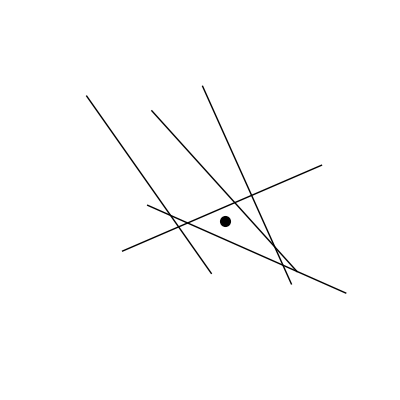

Minimizer location:{0.731765,0.306098}  QEM at minimizer: 0.316159

```mathematica
(* line definition *)
SeedRandom[0];numLines=5;lines=Module[{α},Table[{{Random[],Random[]},α=RandomReal[{0,2π}];{Sin[α],Cos[α]}},{i,numLines}]];
(* call your code to compute QEM coefficients, its minimizer and QEM value *)
{p,e}=getMinimizerQEM2D[getCoefficients2D[lines]];
(* display the minimizer location and its QEM *)
perp[{x_,y_}]:={-y,x};Graphics[{Map[Line[{#⟦1⟧-perp[#⟦2⟧],#⟦1⟧+perp[#⟦2⟧]}]&,lines],PointSize[0.02],Point[p]},PlotRange->{{-1,2},{-1,2}}]
Print["Minimizer location:",p,"  QEM at minimizer: ",e];
```

Algorithm 4: [2 pts] Create a function simplify2D that simplifies an input polyline curve using iterative edge-collapsing until the number of vertices in the polyline is reduced to a given number num.

Notes:
1. Follow the 3-step algorithm as discussed in the lecture. You will need both getCoefficients2D and getMinimizerQEM functions in the first step, in order to compute the initial set of coefficients, minimizer, and QEM at each edge. In the second step, after each edge-collapse, you will only need the getMinimizerQEM function to update the minimizer location and QEM at each re-connected edge. The coefficients at each re-connected edge is updated simply by incrementing the existing coefficients on that edge by the coefficients of the collapsed edge.

2. Collapsing each edge will involve removing the edge and its vertices from the polyline data structure. While removing an edge from the edge list is simple (e.g., using Delete or Drop), removing a vertex from the vertex list will cause the indices of all subsequent vertices to decrement, and hence their references in edges have to be updated. A more efficient way (reminiscent of what you did in thinning) is to simply "tag" a vertex that is being removed during simplification, and apply a single post-process pass to remove all tagged vertices after simplification is done.

```mathematica
simplify2D[curve_,num_]:=
```

Testing: [1 pt] Test your function using the two examples below (a circle and a wavy circle). Follow similar steps as testing your fairing function:

1. Start with a small numPoints (e.g., 10), and gradually go up. Your results should look similar to the pictures below, where the red curves are the original polylines (numPoints=100), and the blue curves are simplified results containing 20 (left) and 10 (right) points respectively in each example.

2. Create a Manipulate applet that allows you to dynamically change the target number of vertices after simplification and displays the result.

```mathematica
(* Circle *)
numPoints=100;
circle={N[Table[{Cos[2π/numPoints*i],Sin[2π/numPoints*i]},{i,numPoints}]],Table[{i,Mod[i,numPoints]+1},{i,numPoints}]};
```

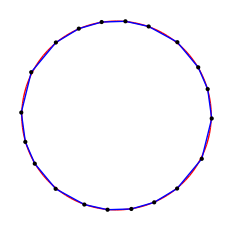
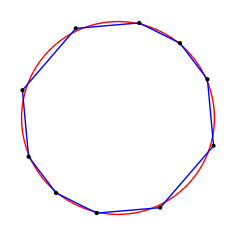

```mathematica
(* Wavy circle *)
numPoints=100;
circleWave={N[Table[{Cos[2π/numPoints*i],Sin[2π/numPoints*i]}*(1+.2*Sin[10π/numPoints*i]),{i,numPoints}]],Table[{i,Mod[i,numPoints]+1},{i,numPoints}]};
```

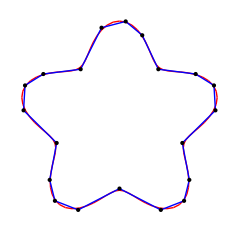
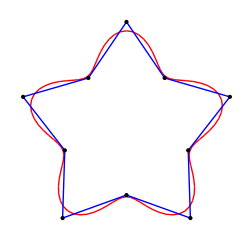

### Simplification (3D) [+6 pts]

Algorithm 5: [Extra credit  2 pts] Create two functions, getCoefficients3D and getMinimizerQEM3D. The function getCoefficients3D takes in a list of 3D planes, each represented as a point on the plane and a (unit) normal vector of the plane, and outputs the three coefficients {a,b,c} in the QEM (see the lecture slides). The function getMinimizerQEM3D takes in three such coefficients, and outputs a pair {p,e} where p is the point location that minimizes the QEM and e is the value of QEM at p. 

Note: If you are clever about creating the 2D versions of these functions, the 3D versions would be identical to them.

```mathematica
getCoefficients3D[planes_]:=
```

```mathematica
getMinimizerQEM3D[{a_,b_,c_}]:=
```

Testing: [Extra credit  1 pt]Test your function using the following code. The code generates a set of random planes, calls your two functions,  displays your computed minimizer location along with the input planes, and prints out the minimizer coordinates and the QEM at the minimizer. Compare your result with the picture and values provided below. Then try with different SeedRandom and numPlanes and make sure your minimizer is always close to the planes.

```mathematica
(* function to display a plane as a quad*)
normalize[v_]:=v/√(v.v);
gPlane[p_,norm_]:=Module[{upvec=normalize[Table[Random[],{3}]],xvec,yvec},
xvec=normalize[Cross[norm,upvec]];yvec=Cross[norm,xvec];
Polygon[Table[2*(Sin[α]xvec+Cos[α]yvec)+p,{α,0,2π,2π/4}]]];
```

```mathematica
(* plane definition *)
SeedRandom[0];numPlanes=3;
planes=Module[{α,β},Table[{{Random[],Random[],Random[]},
α=RandomReal[{0,2π}];β=RandomReal[{-π/2,π/2}];
{Sin[β]Sin[α],Sin[β]Cos[α],Cos[β]}},{i,numPlanes}]];
(* call your code to compute QEM coefficients, its minimizer and QEM value *)
{p,e}=getMinimizerQEM3D[getCoefficients3D[planes]];
(* display the minimizer location and its QEM *)
Graphics3D[{{Opacity[.5],Map[gPlane[#⟦1⟧,#⟦2⟧]&,planes]},PointSize[0.05],Point[p]},PlotRange->All,Boxed->False,RotationAction->Clip]
Print["Minimizer location:",p,"  QEM at minimizer: ",e];
```

-Graphics3D-

Minimizer location:{-0.207438,-0.4136,0.368081}  QEM at minimizer: 1.11022×10^-16

Algorithm 5: [Extra credit 2 pts] Create a function simplify3D that simplifies an input mesh surface using iterative edge-collapsing until the number of vertices in the mesh is reduced to a given number num.

Same notes for the 2D algorithm.

```mathematica
simplify3D[surface_,num_]:=
```

Testing: [Extra credit  1 pt]Test your function using the spherical meshes in files "sphere_small.txt" and "sphere_big.txt" (load them by Get; they are already in your mesh format). Follow similar steps as testing your 2D function:

1. Debug your code first with the small bumpy sphere then with the larger sphere. Your result should look like the pictures below, where the red surfaces and wireframes are the original spheres (first row: small sphere; second row: large sphere), and the gray surfaces have been simplified down to 20 vertices each.

2. Create a Manipulate applet that allows you to dynamically change the target number of vertices after simplification and displays the result.

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
-Graphics3D--Graphics3D-
```

## Problems

Problem 1: [2 pts] The "bone_2D.txt" file contains an iso-curve extracted from a segmented CT image of foot bones (red curve below). Since the segmented image is a binary image, the iso-curve looks zig-zagging. Apply your fairing function to produce a smoother curve (like the blue curve below), and then simplify it down to just one tenth (1/10) of the original number of vertices (like the green curve below). You can load in the file using Get command; it is already in your polyline format.

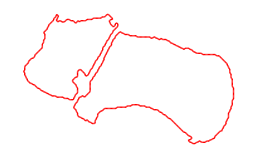
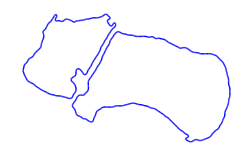
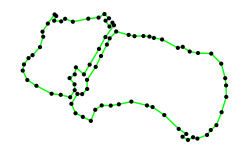

```mathematica
bone2D=Get["bone_2D.txt"];
```

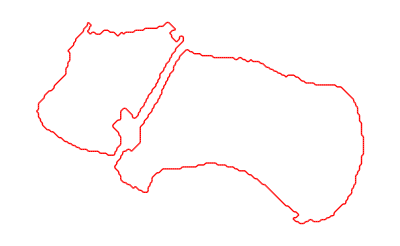

```mathematica
showCurveNoPoints[bone2D,Red]
```

```mathematica
fairBone2D=fair2D[bone2D,0.5,0.1,50];
```

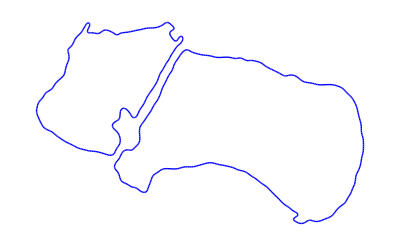

```mathematica
showCurveNoPoints[fairBone2D,Blue]
```

Problem 2: [1 pt, Extra credit 1 pt] The "bone_3D.txt" file contains an iso-surface extracted from a segmented CT image of a single foot bone (picture on the left), which looks zig-zagging. Apply your fairing function to produce a smoother surface (like the one in the middle), and then simplify it down to just one tenth (1/10) of the original number of vertices (like the one on the right). You can load in the file using Get command; it is already in your mesh format.

```mathematica
-Graphics3D--Graphics3D--Graphics3D-
```

```mathematica
bone3D=Get["bone_3D.txt"];
```

```mathematica
showSurfaceNoEdges[bone3D,Gray]
```

-Graphics3D-

```mathematica
fairBone3D=fair3D[bone3D,0.5,0.1,10];//AbsoluteTiming
```

{50.2877,Null}

```mathematica
showSurfaceNoEdges[fairBone3D,Gray]
```

-Graphics3D-